```mathematica
Exit[]
```

```mathematica
a={1,2,3,4,5};b={3,3.1,4,4.5,5};A=4;B=4;
```

```mathematica
Exps[x_]:=Normal[Series[Exp[xx],{xx,0,100}]]/.xx->x
```

```mathematica
p[i_,x_]:=Exps[a[[i]]*x[[1]]+b[[i]]*x[[2]]];Z[x_]:=Sum[p[i,x],{i,1,5}];
```

```mathematica
f[x_]:=Simplify[{Sum[a[[i]]*p[i,x],{i,1,5}]/A-Z[x],Sum[b[[i]]*p[i,x],{i,1,5}]/B-Z[x]}];
```

```mathematica
NSolve[f[{x1,x2}]==0,{x1,x2}]
```

Hold[Abort[],Abort[]]

```mathematica
f[{10,2}]
```

{2.85502×10^25,2.85504×10^25}

```mathematica
J[x_]:=Simplify[Transpose[{D[f[{x1,x2}],x1],D[f[{x1,x2}],x2]}]]/.x1->x[[1]]/.x2->x[[2]]
```

```mathematica
x={0.4,0.3};f[x]
While[ Sqrt[f[x].f[x]]>0.001,
Print[f[x],x];
x-=LinearSolve[J[x],-f[x]]
]
```

{-0.0492306,8.48064}{0.4,0.3}

$Aborted

{-0.0492306,8.48064}

{-0.00271413,0.467545}

{-0.00271413,0.467545}{0.4,0.3}

{-1.99999,-0.899993}{29.9115,-53.8272}

{1.,1.}{6.26379×10^7,-9.85703×10^7}

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: "unfl" will be suppressed during this calculation.

```mathematica
nN=100;h=0.002;
```

```mathematica
M=Table[Table[f[{i,j}*h].f[{i,j}*h],{i,-nN,nN}],{j,-nN,nN}];
```

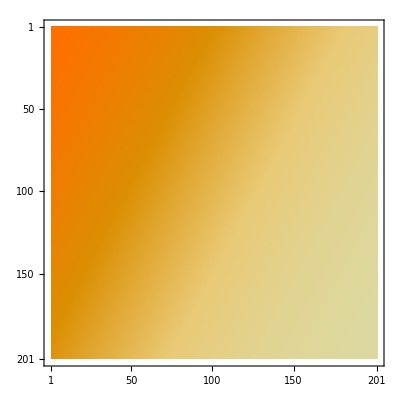

```mathematica
MatrixPlot[M]
```

```mathematica
M//MatrixForm
```

(0.0418833 | 0.0151702 | 0.0109579 | 0.0205675 | 0.0358083 | 0.0515882 | 0.0656297 | 0.0773084 | 0.0867338 | 0.0942526 | 0.100235 | 0.105002 | 0.108813 | 0.111871 | 0.114333 | 0.11632 | 0.117929 | 0.119235 | 0.120296 | 0.121159 | 0.121862 | 0.122435 | 0.122903 | 0.123285 | 0.123598 | 0.123853 | 0.124061 | 0.124232 | 0.124371 | 0.124486 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.0674849 | 0.0266101 | 0.0108744 | 0.0139867 | 0.0270184 | 0.0430375 | 0.0582905 | 0.0713545 | 0.0820174 | 0.0905436 | 0.0973158 | 0.102695 | 0.10698 | 0.110406 | 0.113157 | 0.115373 | 0.117164 | 0.118614 | 0.119792 | 0.120749 | 0.121528 | 0.122163 | 0.122681 | 0.123104 | 0.123449 | 0.123732 | 0.123962 | 0.124151 | 0.124305 | 0.124431 | 0.124535 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.0999452 | 0.0458572 | 0.0166536 | 0.0103578 | 0.0189505 | 0.0340586 | 0.0501409 | 0.0645863 | 0.0766155 | 0.0862973 | 0.0939872 | 0.100077 | 0.10491 | 0.10876 | 0.111841 | 0.114316 | 0.116311 | 0.117924 | 0.119232 | 0.120294 | 0.121158 | 0.121861 | 0.122435 | 0.122903 | 0.123285 | 0.123598 | 0.123853 | 0.124061 | 0.124232 | 0.124371 | 0.124486 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.137295 | 0.0727562 | 0.0296706 | 0.0113525 | 0.0127464 | 0.0251704 | 0.0413061 | 0.0569556 | 0.0704312 | 0.0814203 | 0.0901742 | 0.097094 | 0.102565 | 0.106904 | 0.110363 | 0.113133 | 0.115359 | 0.117156 | 0.11861 | 0.119789 | 0.120747 | 0.121527 | 0.122163 | 0.122681 | 0.123104 | 0.123449 | 0.123732 | 0.123962 | 0.124151 | 0.124305 | 0.124431 | 0.124535 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.177025 | 0.106022 | 0.0505367 | 0.018632 | 0.00992329 | 0.0172437 | 0.0321086 | 0.0484895 | 0.063381 | 0.0758095 | 0.0857876 | 0.0936766 | 0.099893 | 0.104803 | 0.108699 | 0.111806 | 0.114296 | 0.1163 | 0.117918 | 0.119228 | 0.120292 | 0.121157 | 0.121861 | 0.122435 | 0.122903 | 0.123285 | 0.123598 | 0.123853 | 0.124061 | 0.124232 | 0.124371 | 0.124486 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.216645 | 0.143481 | 0.0787697 | 0.0334104 | 0.0122134 | 0.0115564 | 0.0231664 | 0.0393564 | 0.0554244 | 0.0693615 | 0.0807247 | 0.0897424 | 0.0968344 | 0.102412 | 0.106816 | 0.110313 | 0.113104 | 0.115343 | 0.117147 | 0.118605 | 0.119786 | 0.120746 | 0.121526 | 0.122162 | 0.122681 | 0.123104 | 0.123449 | 0.123732 | 0.123962 | 0.124151 | 0.124305 | 0.124431 | 0.124535 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.254125 | 0.182577 | 0.11278 | 0.0560021 | 0.021218 | 0.00974342 | 0.015485 | 0.0299565 | 0.0466149 | 0.0619925 | 0.0748735 | 0.085193 | 0.0933134 | 0.0996769 | 0.104677 | 0.108626 | 0.111764 | 0.114272 | 0.116287 | 0.117911 | 0.119224 | 0.12029 | 0.121156 | 0.12186 | 0.122434 | 0.122903 | 0.123285 | 0.123597 | 0.123853 | 0.124061 | 0.124232 | 0.124371 | 0.124486 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.288121 | 0.220922 | 0.150213 | 0.0855674 | 0.0379331 | 0.0135727 | 0.0104906 | 0.0210277 | 0.037177 | 0.0536751 | 0.068125 | 0.0799153 | 0.0892382 | 0.0965305 | 0.102233 | 0.106712 | 0.110253 | 0.11307 | 0.115324 | 0.117136 | 0.118599 | 0.119783 | 0.120744 | 0.121525 | 0.122162 | 0.12268 | 0.123104 | 0.123449 | 0.123731 | 0.123962 | 0.124151 | 0.124305 | 0.124431 | 0.124535 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.317967 | 0.256685 | 0.18851 | 0.120217 | 0.0623238 | 0.0245335 | 0.00992774 | 0.0137301 | 0.0276088 | 0.0444993 | 0.0603982 | 0.0737885 | 0.0845 | 0.0928887 | 0.099424 | 0.104529 | 0.108541 | 0.111716 | 0.114245 | 0.116271 | 0.117902 | 0.119219 | 0.120287 | 0.121154 | 0.121859 | 0.122434 | 0.122903 | 0.123285 | 0.123597 | 0.123853 | 0.124061 | 0.124232 | 0.124371 | 0.124486 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.343542 | 0.288742 | 0.225426 | 0.157458 | 0.093172 | 0.0433383 | 0.0155616 | 0.00964496 | 0.018791 | 0.0347629 | 0.0516861 | 0.0666993 | 0.0789749 | 0.0886498 | 0.096175 | 0.102023 | 0.106591 | 0.110184 | 0.113031 | 0.115302 | 0.117124 | 0.118592 | 0.119779 | 0.120742 | 0.121524 | 0.122161 | 0.12268 | 0.123103 | 0.123449 | 0.123731 | 0.123962 | 0.124151 | 0.124305 | 0.124431 | 0.124535 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.365086 | 0.31662 | 0.259356 | 0.194776 | 0.128312 | 0.0695547 | 0.0287036 | 0.0106065 | 0.0120561 | 0.0250845 | 0.0421287 | 0.0585746 | 0.0725334 | 0.0836932 | 0.0923927 | 0.0991279 | 0.104356 | 0.108441 | 0.111659 | 0.114213 | 0.116253 | 0.117892 | 0.119214 | 0.120284 | 0.121152 | 0.121858 | 0.122433 | 0.122902 | 0.123285 | 0.123597 | 0.123853 | 0.124061 | 0.124232 | 0.124371 | 0.124486 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.383034 | 0.340331 | 0.289403 | 0.230113 | 0.165162 | 0.10158 | 0.0497134 | 0.0183226 | 0.00913916 | 0.016512 | 0.0321175 | 0.0494373 | 0.0650608 | 0.0778841 | 0.0879638 | 0.0957594 | 0.101778 | 0.106448 | 0.110102 | 0.112984 | 0.115276 | 0.117109 | 0.118584 | 0.119775 | 0.120739 | 0.121523 | 0.12216 | 0.12268 | 0.123103 | 0.123449 | 0.123731 | 0.123962 | 0.124151 | 0.124305 | 0.124431 | 0.124535 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.397898 | 0.360193 | 0.315279 | 0.262108 | 0.201311 | 0.137014 | 0.0777224 | 0.0338487 | 0.0119286 | 0.0105644 | 0.022418 | 0.0394945 | 0.0564981 | 0.0710852 | 0.0827555 | 0.0918136 | 0.0987815 | 0.104153 | 0.108324 | 0.111592 | 0.114175 | 0.116232 | 0.11788 | 0.119207 | 0.12028 | 0.12115 | 0.121857 | 0.122433 | 0.122902 | 0.123285 | 0.123597 | 0.123853 | 0.124061 | 0.124232 | 0.124371 | 0.124486 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.410186 | 0.376679 | 0.337122 | 0.290097 | 0.234927 | 0.17325 | 0.110759 | 0.0571237 | 0.0220026 | 0.00911675 | 0.0142695 | 0.0292565 | 0.0469116 | 0.0631844 | 0.0766216 | 0.0871649 | 0.0952737 | 0.10149 | 0.106281 | 0.110006 | 0.11293 | 0.115245 | 0.117092 | 0.118574 | 0.119769 | 0.120736 | 0.121521 | 0.122159 | 0.122679 | 0.123103 | 0.123449 | 0.123731 | 0.123962 | 0.124151 | 0.124305 | 0.124431 | 0.124535 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.420364 | 0.390301 | 0.355318 | 0.313964 | 0.264908 | 0.20804 | 0.146246 | 0.0868218 | 0.0400744 | 0.0140567 | 0.00938311 | 0.0196641 | 0.0365969 | 0.0541463 | 0.0694191 | 0.0816673 | 0.0911384 | 0.0983764 | 0.103915 | 0.108187 | 0.111514 | 0.114131 | 0.116207 | 0.117866 | 0.1192 | 0.120276 | 0.121148 | 0.121856 | 0.122432 | 0.122902 | 0.123284 | 0.123597 | 0.123852 | 0.124061 | 0.124232 | 0.124371 | 0.124486 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.428834 | 0.401554 | 0.370362 | 0.333959 | 0.290813 | 0.239809 | 0.18163 | 0.120642 | 0.0656032 | 0.0267434 | 0.0097428 | 0.0121687 | 0.0262117 | 0.0440975 | 0.0610448 | 0.0751636 | 0.0862359 | 0.0947067 | 0.101154 | 0.106086 | 0.109894 | 0.112866 | 0.115209 | 0.117072 | 0.118563 | 0.119763 | 0.120733 | 0.121519 | 0.122158 | 0.122678 | 0.123103 | 0.123449 | 0.123731 | 0.123962 | 0.124151 | 0.124305 | 0.124431 | 0.124535 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.435932 | 0.410878 | 0.382766 | 0.350523 | 0.31269 | 0.267719 | 0.214876 | 0.155908 | 0.09681 | 0.0474597 | 0.0171589 | 0.00866697 | 0.0169019 | 0.033448 | 0.0514994 | 0.0675091 | 0.0804068 | 0.0903517 | 0.0979029 | 0.103637 | 0.108026 | 0.111422 | 0.114079 | 0.116178 | 0.11785 | 0.11919 | 0.120271 | 0.121145 | 0.121854 | 0.122431 | 0.122901 | 0.123284 | 0.123597 | 0.123852 | 0.124061 | 0.124232 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.441935 | 0.418651 | 0.393003 | 0.364165 | 0.330879 | 0.291544 | 0.244693 | 0.190193 | 0.131129 | 0.0751457 | 0.0326693 | 0.0111985 | 0.010344 | 0.0230357 | 0.0409914 | 0.0586175 | 0.0734848 | 0.0851572 | 0.0940452 | 0.10076 | 0.105856 | 0.109762 | 0.112791 | 0.115167 | 0.117048 | 0.11855 | 0.119756 | 0.120729 | 0.121517 | 0.122157 | 0.122678 | 0.123102 | 0.123448 | 0.123731 | 0.123962 | 0.124151 | 0.124305 | 0.124431 | 0.124535 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.447066 | 0.425183 | 0.40149 | 0.375387 | 0.345864 | 0.31147 | 0.270504 | 0.221729 | 0.165875 | 0.107603 | 0.0560458 | 0.0213979 | 0.00859525 | 0.0142386 | 0.0300765 | 0.0485426 | 0.0653282 | 0.0789502 | 0.0894365 | 0.0973499 | 0.103312 | 0.107838 | 0.111315 | 0.114018 | 0.116144 | 0.117831 | 0.11918 | 0.120265 | 0.121142 | 0.121853 | 0.12243 | 0.122901 | 0.123284 | 0.123597 | 0.123852 | 0.124061 | 0.124232 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.451502 | 0.430728 | 0.408576 | 0.384641 | 0.35816 | 0.327918 | 0.292277 | 0.249517 | 0.198824 | 0.142089 | 0.0856988 | 0.0398736 | 0.0136721 | 0.0089593 | 0.0198066 | 0.0376018 | 0.0558802 | 0.071558 | 0.083907 | 0.0932743 | 0.100301 | 0.105588 | 0.109608 | 0.112704 | 0.115118 | 0.11702 | 0.118534 | 0.119747 | 0.120724 | 0.121514 | 0.122156 | 0.122677 | 0.123102 | 0.123448 | 0.123731 | 0.123962 | 0.124151 | 0.124305 | 0.124431 | 0.124535 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.455386 | 0.435489 | 0.414548 | 0.392317 | 0.368251 | 0.341395 | 0.310318 | 0.273229 | 0.228506 | 0.176008 | 0.119077 | 0.0658263 | 0.0269168 | 0.00936576 | 0.0118128 | 0.0265318 | 0.0452691 | 0.0628501 | 0.0772714 | 0.0883733 | 0.0967047 | 0.102931 | 0.107618 | 0.111189 | 0.113947 | 0.116103 | 0.117808 | 0.119167 | 0.120258 | 0.121138 | 0.12185 | 0.122429 | 0.1229 | 0.123284 | 0.123597 | 0.123852 | 0.124061 | 0.124232 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.45883 | 0.439629 | 0.419636 | 0.398736 | 0.376567 | 0.352412 | 0.325104 | 0.293002 | 0.254219 | 0.207401 | 0.153369 | 0.0971619 | 0.0484058 | 0.0173463 | 0.00820559 | 0.0166319 | 0.0339535 | 0.0528151 | 0.0693552 | 0.0824612 | 0.0923771 | 0.0997633 | 0.105274 | 0.109427 | 0.112601 | 0.11506 | 0.116988 | 0.118516 | 0.119737 | 0.120718 | 0.121511 | 0.122154 | 0.122676 | 0.123101 | 0.123448 | 0.123731 | 0.123962 | 0.124151 | 0.124305 | 0.124431 | 0.124535 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.461922 | 0.443275 | 0.424025 | 0.40416 | 0.383467 | 0.361435 | 0.337157 | 0.309242 | 0.275859 | 0.235121 | 0.186161 | 0.131074 | 0.0767406 | 0.0338238 | 0.0111851 | 0.00979494 | 0.0228897 | 0.0416833 | 0.0600503 | 0.0753426 | 0.0871403 | 0.0959525 | 0.102486 | 0.107359 | 0.111041 | 0.113863 | 0.116056 | 0.117782 | 0.119153 | 0.12025 | 0.121133 | 0.121848 | 0.122428 | 0.122899 | 0.123283 | 0.123596 | 0.123852 | 0.124061 | 0.124232 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.464732 | 0.446527 | 0.427861 | 0.408798 | 0.389246 | 0.368864 | 0.346975 | 0.322461 | 0.29371 | 0.258745 | 0.215811 | 0.164799 | 0.109389 | 0.0582603 | 0.0223828 | 0.0082951 | 0.0136523 | 0.0300922 | 0.049412 | 0.0668484 | 0.0807935 | 0.0913342 | 0.0991363 | 0.104906 | 0.109216 | 0.11248 | 0.114991 | 0.11695 | 0.118495 | 0.119725 | 0.120712 | 0.121508 | 0.122152 | 0.122675 | 0.123101 | 0.123448 | 0.123731 | 0.123962 | 0.124151 | 0.124305 | 0.124431 | 0.124535 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.467317 | 0.449468 | 0.431258 | 0.412817 | 0.394142 | 0.375031 | 0.354999 | 0.333183 | 0.308247 | 0.278369 | 0.241495 | 0.196189 | 0.143412 | 0.0886724 | 0.0421776 | 0.0142551 | 0.00838548 | 0.0192562 | 0.0378057 | 0.0569083 | 0.0731348 | 0.0857133 | 0.0950766 | 0.101966 | 0.107057 | 0.110868 | 0.113765 | 0.116001 | 0.117751 | 0.119135 | 0.12024 | 0.121128 | 0.121845 | 0.122426 | 0.122898 | 0.123283 | 0.123596 | 0.123852 | 0.124061 | 0.124232 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.46972 | 0.452158 | 0.434308 | 0.416347 | 0.398343 | 0.380203 | 0.361601 | 0.341888 | 0.320004 | 0.294392 | 0.263049 | 0.223946 | 0.176207 | 0.122195 | 0.0693699 | 0.0289052 | 0.00945095 | 0.0110424 | 0.02609 | 0.0456713 | 0.064011 | 0.0788754 | 0.0901242 | 0.0984051 | 0.104477 | 0.108968 | 0.112339 | 0.114912 | 0.116905 | 0.11847 | 0.119711 | 0.120704 | 0.121503 | 0.122149 | 0.122674 | 0.1231 | 0.123447 | 0.12373 | 0.123962 | 0.124151 | 0.124305 | 0.124431 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.471975 | 0.454648 | 0.437083 | 0.41949 | 0.401998 | 0.384596 | 0.367082 | 0.348989 | 0.329496 | 0.307336 | 0.280736 | 0.247561 | 0.205956 | 0.155892 | 0.101454 | 0.0519753 | 0.0187556 | 0.00780862 | 0.0157722 | 0.0336776 | 0.0534101 | 0.0706186 | 0.084066 | 0.0940582 | 0.101358 | 0.106703 | 0.110665 | 0.11365 | 0.115936 | 0.117715 | 0.119115 | 0.120229 | 0.121122 | 0.121842 | 0.122424 | 0.122897 | 0.123282 | 0.123596 | 0.123852 | 0.124061 | 0.124232 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.474111 | 0.456977 | 0.439637 | 0.422329 | 0.405224 | 0.388378 | 0.371687 | 0.354826 | 0.337179 | 0.317743 | 0.295039 | 0.267095 | 0.231717 | 0.187424 | 0.135368 | 0.0816051 | 0.0369829 | 0.0118926 | 0.00900947 | 0.0220502 | 0.0416088 | 0.0608199 | 0.0766773 | 0.0887228 | 0.0975533 | 0.103974 | 0.108677 | 0.112173 | 0.114818 | 0.116852 | 0.11844 | 0.119695 | 0.120695 | 0.121498 | 0.122147 | 0.122672 | 0.123099 | 0.123447 | 0.12373 | 0.123961 | 0.12415 | 0.124305 | 0.124431 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.47615 | 0.459177 | 0.442016 | 0.424926 | 0.408112 | 0.391682 | 0.375606 | 0.359675 | 0.343433 | 0.326109 | 0.30651 | 0.282944 | 0.253268 | 0.215343 | 0.168314 | 0.114877 | 0.0631457 | 0.0248262 | 0.00830195 | 0.0126141 | 0.0293664 | 0.0495524 | 0.0677656 | 0.0821695 | 0.0928757 | 0.10065 | 0.106289 | 0.110427 | 0.113515 | 0.11586 | 0.117672 | 0.119091 | 0.120216 | 0.121115 | 0.121838 | 0.122422 | 0.122896 | 0.123281 | 0.123595 | 0.123852 | 0.124061 | 0.124232 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.478109 | 0.461273 | 0.444254 | 0.427331 | 0.410734 | 0.39461 | 0.378991 | 0.363753 | 0.348571 | 0.33286 | 0.315681 | 0.295647 | 0.270859 | 0.239051 | 0.198296 | 0.148685 | 0.0947796 | 0.0466179 | 0.0158179 | 0.00778731 | 0.0181114 | 0.0372608 | 0.057258 | 0.0741686 | 0.0871036 | 0.0965623 | 0.103388 | 0.108337 | 0.111979 | 0.114708 | 0.116791 | 0.118406 | 0.119676 | 0.120684 | 0.121492 | 0.122143 | 0.12267 | 0.123098 | 0.123446 | 0.12373 | 0.123961 | 0.12415 | 0.124305 | 0.124431 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.480003 | 0.463284 | 0.446381 | 0.429584 | 0.413146 | 0.397245 | 0.381958 | 0.367231 | 0.352841 | 0.338346 | 0.323024 | 0.305766 | 0.284982 | 0.258579 | 0.224249 | 0.180492 | 0.128703 | 0.0755485 | 0.0325486 | 0.0101013 | 0.00999347 | 0.0249712 | 0.0453461 | 0.0645504 | 0.0799936 | 0.0915054 | 0.0998241 | 0.105806 | 0.110149 | 0.113357 | 0.115771 | 0.117622 | 0.119063 | 0.1202 | 0.121106 | 0.121833 | 0.122419 | 0.122894 | 0.123281 | 0.123595 | 0.123851 | 0.124061 | 0.124231 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.481843 | 0.465225 | 0.448416 | 0.431716 | 0.415392 | 0.399648 | 0.3846 | 0.370244 | 0.356435 | 0.34285 | 0.328933 | 0.313815 | 0.296212 | 0.274325 | 0.245895 | 0.208692 | 0.161923 | 0.108662 | 0.0577377 | 0.021383 | 0.00762591 | 0.0144502 | 0.0326893 | 0.0533177 | 0.0713193 | 0.0852379 | 0.0954112 | 0.102703 | 0.10794 | 0.111752 | 0.11458 | 0.116718 | 0.118365 | 0.119653 | 0.120672 | 0.121485 | 0.12214 | 0.122668 | 0.123097 | 0.123445 | 0.123729 | 0.123961 | 0.12415 | 0.124305 | 0.124431 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.483638 | 0.46711 | 0.450379 | 0.433751 | 0.417506 | 0.40187 | 0.386986 | 0.372894 | 0.359508 | 0.346594 | 0.333728 | 0.320237 | 0.305101 | 0.286847 | 0.263472 | 0.232601 | 0.192254 | 0.142684 | 0.0889819 | 0.0419324 | 0.013422 | 0.00815133 | 0.0206271 | 0.0408221 | 0.0609527 | 0.0775069 | 0.0899209 | 0.0988631 | 0.105241 | 0.109823 | 0.113171 | 0.115667 | 0.117563 | 0.119031 | 0.120182 | 0.121096 | 0.121827 | 0.122416 | 0.122893 | 0.12328 | 0.123594 | 0.123851 | 0.12406 | 0.124231 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.485394 | 0.468949 | 0.452283 | 0.435709 | 0.419517 | 0.40395 | 0.389174 | 0.375262 | 0.362176 | 0.349749 | 0.337662 | 0.325392 | 0.312141 | 0.29673 | 0.277487 | 0.252215 | 0.218509 | 0.174873 | 0.122992 | 0.070195 | 0.0286839 | 0.00877605 | 0.0112799 | 0.0279879 | 0.0490054 | 0.0681018 | 0.0830948 | 0.0940764 | 0.101905 | 0.107475 | 0.111486 | 0.114429 | 0.116634 | 0.118318 | 0.119627 | 0.120657 | 0.121477 | 0.122135 | 0.122666 | 0.123096 | 0.123445 | 0.123729 | 0.123961 | 0.12415 | 0.124305 | 0.124431 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.487119 | 0.470749 | 0.454139 | 0.437605 | 0.421446 | 0.405918 | 0.391206 | 0.37741 | 0.364529 | 0.352451 | 0.340933 | 0.329569 | 0.317738 | 0.304511 | 0.288538 | 0.267937 | 0.240347 | 0.203463 | 0.156575 | 0.103195 | 0.0529072 | 0.0184375 | 0.00734789 | 0.0165081 | 0.0360362 | 0.0569611 | 0.074678 | 0.0880934 | 0.0977463 | 0.104581 | 0.109442 | 0.112954 | 0.115544 | 0.117495 | 0.118992 | 0.120161 | 0.121084 | 0.121821 | 0.122413 | 0.122891 | 0.123279 | 0.123594 | 0.123851 | 0.12406 | 0.124231 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.488816 | 0.472518 | 0.455956 | 0.439451 | 0.42331 | 0.407797 | 0.393116 | 0.379388 | 0.36664 | 0.354803 | 0.343692 | 0.332994 | 0.322221 | 0.310647 | 0.297203 | 0.280349 | 0.257996 | 0.22767 | 0.187355 | 0.137498 | 0.0837758 | 0.0377403 | 0.0114698 | 0.00884617 | 0.0232867 | 0.0443459 | 0.0644932 | 0.0806424 | 0.0925317 | 0.100976 | 0.106932 | 0.111174 | 0.114252 | 0.116534 | 0.118262 | 0.119596 | 0.12064 | 0.121468 | 0.12213 | 0.122663 | 0.123094 | 0.123444 | 0.123729 | 0.123961 | 0.12415 | 0.124305 | 0.124431 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.49049 | 0.47426 | 0.457742 | 0.441259 | 0.425122 | 0.409608 | 0.394932 | 0.381232 | 0.368562 | 0.356883 | 0.346058 | 0.335841 | 0.325849 | 0.315511 | 0.303991 | 0.29006 | 0.271979 | 0.247459 | 0.214007 | 0.170152 | 0.117908 | 0.0653223 | 0.0252595 | 0.00784726 | 0.0128275 | 0.0310757 | 0.052577 | 0.0714774 | 0.085992 | 0.0964504 | 0.103812 | 0.108996 | 0.1127 | 0.1154 | 0.117414 | 0.118947 | 0.120136 | 0.12107 | 0.121813 | 0.122408 | 0.122888 | 0.123277 | 0.123593 | 0.12385 | 0.12406 | 0.124231 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.492143 | 0.475979 | 0.459501 | 0.443034 | 0.426894 | 0.411364 | 0.396673 | 0.382973 | 0.370338 | 0.358755 | 0.348122 | 0.338246 | 0.328822 | 0.3194 | 0.309323 | 0.29763 | 0.28292 | 0.263238 | 0.236127 | 0.199219 | 0.151916 | 0.098214 | 0.0484874 | 0.0158985 | 0.00741736 | 0.0187555 | 0.0393888 | 0.0604781 | 0.0778482 | 0.0907486 | 0.0998957 | 0.106298 | 0.110809 | 0.114045 | 0.116418 | 0.118197 | 0.119559 | 0.12062 | 0.121457 | 0.122124 | 0.122659 | 0.123092 | 0.123443 | 0.123728 | 0.12396 | 0.12415 | 0.124305 | 0.124431 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.493778 | 0.477678 | 0.46124 | 0.444785 | 0.428634 | 0.413079 | 0.398356 | 0.384634 | 0.372001 | 0.360465 | 0.349953 | 0.340311 | 0.331294 | 0.322542 | 0.313539 | 0.303533 | 0.291421 | 0.27561 | 0.25393 | 0.223813 | 0.18322 | 0.132829 | 0.0789554 | 0.0339211 | 0.00989758 | 0.00983318 | 0.0260643 | 0.0478195 | 0.0678796 | 0.0835842 | 0.0949497 | 0.102916 | 0.108475 | 0.112402 | 0.115232 | 0.11732 | 0.118895 | 0.120107 | 0.121054 | 0.121804 | 0.122403 | 0.122886 | 0.123276 | 0.123592 | 0.12385 | 0.12406 | 0.124231 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.495397 | 0.479362 | 0.46296 | 0.446515 | 0.430349 | 0.414761 | 0.399995 | 0.386233 | 0.373576 | 0.36205 | 0.351605 | 0.342116 | 0.333384 | 0.325117 | 0.316904 | 0.308156 | 0.298012 | 0.285213 | 0.267955 | 0.243859 | 0.210352 | 0.166005 | 0.113211 | 0.0607753 | 0.0221914 | 0.00726918 | 0.014605 | 0.0342139 | 0.0560532 | 0.074681 | 0.0886962 | 0.0986413 | 0.105558 | 0.110382 | 0.113802 | 0.116281 | 0.118121 | 0.119517 | 0.120596 | 0.121444 | 0.122116 | 0.122655 | 0.12309 | 0.123442 | 0.123727 | 0.12396 | 0.12415 | 0.124304 | 0.124431 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.497 | 0.48103 | 0.464665 | 0.448228 | 0.432045 | 0.416418 | 0.401601 | 0.387784 | 0.375083 | 0.363539 | 0.353118 | 0.343721 | 0.33518 | 0.327258 | 0.31962 | 0.311802 | 0.303133 | 0.292629 | 0.27885 | 0.259769 | 0.232835 | 0.195621 | 0.147676 | 0.0935283 | 0.0443665 | 0.0137084 | 0.0077993 | 0.0211659 | 0.0427312 | 0.0638658 | 0.0808368 | 0.0932159 | 0.101873 | 0.107867 | 0.112053 | 0.115035 | 0.117209 | 0.118833 | 0.120072 | 0.121035 | 0.121793 | 0.122398 | 0.122882 | 0.123274 | 0.123591 | 0.123849 | 0.124059 | 0.124231 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.498591 | 0.482686 | 0.466358 | 0.449929 | 0.433726 | 0.418056 | 0.40318 | 0.3893 | 0.37654 | 0.364954 | 0.354525 | 0.345172 | 0.336753 | 0.329068 | 0.321844 | 0.314707 | 0.307131 | 0.298353 | 0.287247 | 0.272169 | 0.250866 | 0.220678 | 0.179559 | 0.128458 | 0.0743772 | 0.0303973 | 0.00866488 | 0.0110833 | 0.0289376 | 0.0512319 | 0.071113 | 0.0863416 | 0.0971878 | 0.104696 | 0.109884 | 0.113518 | 0.116121 | 0.118031 | 0.119467 | 0.120568 | 0.121428 | 0.122108 | 0.122651 | 0.123087 | 0.12344 | 0.123727 | 0.123959 | 0.124149 | 0.124304 | 0.124431 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.500168 | 0.48433 | 0.46804 | 0.451619 | 0.435395 | 0.419679 | 0.404741 | 0.390788 | 0.377957 | 0.366313 | 0.355851 | 0.346505 | 0.338154 | 0.330627 | 0.323694 | 0.31705 | 0.310278 | 0.302784 | 0.293697 | 0.281723 | 0.265 | 0.241056 | 0.20724 | 0.162192 | 0.108728 | 0.0564503 | 0.0194277 | 0.0070113 | 0.0165869 | 0.0373844 | 0.059428 | 0.0777172 | 0.0912182 | 0.100663 | 0.107157 | 0.111645 | 0.114803 | 0.117079 | 0.11876 | 0.120032 | 0.121012 | 0.121781 | 0.122391 | 0.122879 | 0.123272 | 0.12359 | 0.123849 | 0.124059 | 0.124231 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.501734 | 0.485963 | 0.469713 | 0.4533 | 0.437055 | 0.421293 | 0.406288 | 0.392257 | 0.379346 | 0.36763 | 0.357114 | 0.347747 | 0.339424 | 0.331994 | 0.325259 | 0.318967 | 0.312781 | 0.306235 | 0.298655 | 0.289041 | 0.275911 | 0.257166 | 0.230157 | 0.192413 | 0.143657 | 0.0890062 | 0.0404732 | 0.0118321 | 0.00846811 | 0.0237166 | 0.0460497 | 0.0671222 | 0.083651 | 0.0955071 | 0.103693 | 0.109301 | 0.113185 | 0.115933 | 0.117926 | 0.119408 | 0.120536 | 0.12141 | 0.122098 | 0.122645 | 0.123084 | 0.123438 | 0.123726 | 0.123959 | 0.124149 | 0.124304 | 0.124431 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.503288 | 0.487587 | 0.471377 | 0.454975 | 0.438709 | 0.422899 | 0.407826 | 0.393712 | 0.380714 | 0.368914 | 0.358331 | 0.348921 | 0.340593 | 0.333213 | 0.326609 | 0.320563 | 0.314799 | 0.308946 | 0.302481 | 0.294635 | 0.284258 | 0.269654 | 0.248485 | 0.217999 | 0.176159 | 0.124229 | 0.0699455 | 0.0271226 | 0.00774636 | 0.0125732 | 0.0318867 | 0.0545738 | 0.0741953 | 0.0889237 | 0.0992584 | 0.106329 | 0.111169 | 0.114533 | 0.116927 | 0.118675 | 0.119984 | 0.120986 | 0.121766 | 0.122383 | 0.122874 | 0.123269 | 0.123589 | 0.123848 | 0.124059 | 0.12423 | 0.124371 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.504831 | 0.489201 | 0.473034 | 0.456643 | 0.440358 | 0.424501 | 0.409357 | 0.395158 | 0.382067 | 0.370176 | 0.359513 | 0.350043 | 0.341686 | 0.33432 | 0.327793 | 0.321914 | 0.31645 | 0.3111 | 0.305454 | 0.29892 | 0.290616 | 0.279215 | 0.26279 | 0.238774 | 0.204444 | 0.158535 | 0.104338 | 0.0522822 | 0.0169388 | 0.00705253 | 0.0187508 | 0.0405705 | 0.0626962 | 0.0805908 | 0.0935687 | 0.102526 | 0.108621 | 0.112796 | 0.115713 | 0.117802 | 0.119339 | 0.120498 | 0.121389 | 0.122086 | 0.122639 | 0.123081 | 0.123437 | 0.123725 | 0.123958 | 0.124149 | 0.124304 | 0.124431 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.506364 | 0.490807 | 0.474685 | 0.458307 | 0.442004 | 0.4261 | 0.410885 | 0.396598 | 0.38341 | 0.371422 | 0.360669 | 0.351126 | 0.34272 | 0.335342 | 0.328851 | 0.323079 | 0.317823 | 0.312835 | 0.307786 | 0.302218 | 0.295457 | 0.286483 | 0.273772 | 0.255145 | 0.227858 | 0.189403 | 0.139718 | 0.0845601 | 0.0367663 | 0.0102498 | 0.00940364 | 0.0263866 | 0.0493317 | 0.0702464 | 0.0862983 | 0.0976336 | 0.105366 | 0.110612 | 0.114216 | 0.116748 | 0.118575 | 0.119929 | 0.120955 | 0.121749 | 0.122373 | 0.122869 | 0.123267 | 0.123587 | 0.123847 | 0.124058 | 0.12423 | 0.12437 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.507886 | 0.492404 | 0.476329 | 0.459967 | 0.443648 | 0.427697 | 0.412412 | 0.398035 | 0.384747 | 0.372657 | 0.361807 | 0.35218 | 0.343711 | 0.336299 | 0.329814 | 0.324102 | 0.318987 | 0.314254 | 0.309637 | 0.304776 | 0.299153 | 0.291993 | 0.282119 | 0.26778 | 0.246544 | 0.215574 | 0.172862 | 0.120032 | 0.0656007 | 0.0240727 | 0.00712618 | 0.0142822 | 0.0348932 | 0.0578371 | 0.077129 | 0.0913398 | 0.101173 | 0.107828 | 0.112341 | 0.115455 | 0.117658 | 0.119259 | 0.120453 | 0.121364 | 0.122072 | 0.122631 | 0.123076 | 0.123434 | 0.123723 | 0.123958 | 0.124148 | 0.124304 | 0.124431 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.509398 | 0.493993 | 0.477967 | 0.461623 | 0.44529 | 0.429295 | 0.413939 | 0.399472 | 0.386082 | 0.373886 | 0.362933 | 0.353213 | 0.344669 | 0.337206 | 0.330703 | 0.325019 | 0.319991 | 0.315435 | 0.311127 | 0.30678 | 0.301992 | 0.296173 | 0.28843 | 0.277398 | 0.261077 | 0.236808 | 0.201797 | 0.154908 | 0.0999601 | 0.0482341 | 0.0147105 | 0.00737716 | 0.0210763 | 0.0437574 | 0.065854 | 0.0833072 | 0.0957579 | 0.104245 | 0.109961 | 0.113845 | 0.116539 | 0.118458 | 0.119864 | 0.120919 | 0.121729 | 0.122362 | 0.122863 | 0.123263 | 0.123585 | 0.123846 | 0.124058 | 0.12423 | 0.12437 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.5109 | 0.495574 | 0.479599 | 0.463276 | 0.446931 | 0.430893 | 0.415468 | 0.400911 | 0.387417 | 0.375112 | 0.364051 | 0.354232 | 0.345604 | 0.338077 | 0.331538 | 0.325853 | 0.320874 | 0.316435 | 0.312346 | 0.308369 | 0.304189 | 0.299357 | 0.293193 | 0.284661 | 0.272183 | 0.253498 | 0.225763 | 0.186454 | 0.135761 | 0.0801354 | 0.033226 | 0.00895148 | 0.0105886 | 0.0291566 | 0.0525663 | 0.0732383 | 0.0887861 | 0.0996063 | 0.106904 | 0.111809 | 0.115154 | 0.117488 | 0.119164 | 0.1204 | 0.121335 | 0.122056 | 0.122622 | 0.123072 | 0.123431 | 0.123722 | 0.123957 | 0.124148 | 0.124304 | 0.12443 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.512391 | 0.497147 | 0.481226 | 0.464926 | 0.448571 | 0.432493 | 0.416999 | 0.402353 | 0.388755 | 0.376338 | 0.365166 | 0.355242 | 0.346522 | 0.338921 | 0.332331 | 0.326626 | 0.321666 | 0.3173 | 0.313359 | 0.309647 | 0.305908 | 0.301796 | 0.296796 | 0.290125 | 0.280575 | 0.266329 | 0.244865 | 0.213259 | 0.169556 | 0.115795 | 0.0613099 | 0.0212382 | 0.00679397 | 0.0161914 | 0.0379399 | 0.0610149 | 0.0799173 | 0.0935989 | 0.102944 | 0.109202 | 0.113411 | 0.116294 | 0.118321 | 0.119787 | 0.120877 | 0.121706 | 0.122349 | 0.122856 | 0.123259 | 0.123583 | 0.123845 | 0.124057 | 0.124229 | 0.12437 | 0.124485 | 0.124579 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.513873 | 0.498711 | 0.482848 | 0.466573 | 0.450212 | 0.434095 | 0.418535 | 0.403799 | 0.390096 | 0.377566 | 0.36628 | 0.356247 | 0.347429 | 0.339746 | 0.333094 | 0.327352 | 0.322388 | 0.31806 | 0.314219 | 0.310691 | 0.307271 | 0.303682 | 0.299534 | 0.294236 | 0.286877 | 0.27605 | 0.259679 | 0.235004 | 0.199178 | 0.151224 | 0.0955458 | 0.0442898 | 0.0127383 | 0.00797219 | 0.0235437 | 0.046931 | 0.0688985 | 0.0858722 | 0.0977959 | 0.105829 | 0.111188 | 0.114801 | 0.11729 | 0.119053 | 0.120338 | 0.121301 | 0.122037 | 0.122612 | 0.123066 | 0.123428 | 0.12372 | 0.123956 | 0.124147 | 0.124303 | 0.12443 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.515344 | 0.500268 | 0.484463 | 0.468218 | 0.451852 | 0.4357 | 0.420074 | 0.405251 | 0.391443 | 0.378798 | 0.367396 | 0.357251 | 0.348329 | 0.340557 | 0.333834 | 0.328043 | 0.323057 | 0.318743 | 0.314961 | 0.311561 | 0.308366 | 0.305156 | 0.301628 | 0.297336 | 0.291598 | 0.283348 | 0.270954 | 0.252066 | 0.223747 | 0.183468 | 0.131721 | 0.0757023 | 0.029847 | 0.00793249 | 0.0120067 | 0.0320079 | 0.0557435 | 0.0760986 | 0.0911221 | 0.101436 | 0.108318 | 0.112904 | 0.116007 | 0.11816 | 0.119697 | 0.120827 | 0.121678 | 0.122334 | 0.122847 | 0.123255 | 0.123581 | 0.123843 | 0.124056 | 0.124229 | 0.12437 | 0.124485 | 0.124578 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.516804 | 0.501816 | 0.486074 | 0.469859 | 0.453493 | 0.437307 | 0.421619 | 0.406708 | 0.392796 | 0.380036 | 0.368515 | 0.358255 | 0.349226 | 0.341359 | 0.334558 | 0.328708 | 0.323686 | 0.319366 | 0.315616 | 0.312298 | 0.309261 | 0.306323 | 0.303244 | 0.299687 | 0.295139 | 0.288802 | 0.279432 | 0.265143 | 0.243316 | 0.210947 | 0.166164 | 0.111471 | 0.0570595 | 0.0186199 | 0.00674207 | 0.0182824 | 0.0410106 | 0.0641013 | 0.0825637 | 0.0957098 | 0.10458 | 0.110463 | 0.114387 | 0.117057 | 0.118923 | 0.120266 | 0.121261 | 0.122015 | 0.122599 | 0.123059 | 0.123425 | 0.123718 | 0.123955 | 0.124147 | 0.124303 | 0.12443 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.518255 | 0.503356 | 0.487678 | 0.471498 | 0.455134 | 0.438917 | 0.423168 | 0.408172 | 0.394156 | 0.381281 | 0.36964 | 0.359263 | 0.350123 | 0.342157 | 0.335271 | 0.329354 | 0.324286 | 0.319944 | 0.316203 | 0.312936 | 0.310006 | 0.30726 | 0.304507 | 0.301483 | 0.297803 | 0.292874 | 0.285761 | 0.275009 | 0.258461 | 0.233255 | 0.196502 | 0.147424 | 0.0910677 | 0.0404475 | 0.0110234 | 0.00882566 | 0.0261342 | 0.0500788 | 0.0718278 | 0.0882917 | 0.0996922 | 0.107289 | 0.112312 | 0.115672 | 0.117972 | 0.119592 | 0.120769 | 0.121646 | 0.122316 | 0.122837 | 0.123249 | 0.123578 | 0.123842 | 0.124055 | 0.124229 | 0.12437 | 0.124485 | 0.124578 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.519694 | 0.504887 | 0.489277 | 0.473134 | 0.456775 | 0.44053 | 0.424723 | 0.409643 | 0.395524 | 0.382534 | 0.370772 | 0.360275 | 0.351023 | 0.342954 | 0.335978 | 0.329987 | 0.324865 | 0.320489 | 0.31674 | 0.313498 | 0.310638 | 0.308027 | 0.305505 | 0.302868 | 0.29982 | 0.29592 | 0.290472 | 0.282379 | 0.269949 | 0.250739 | 0.221717 | 0.180376 | 0.127556 | 0.0712493 | 0.0266346 | 0.00719117 | 0.0136423 | 0.0349228 | 0.0588547 | 0.0788287 | 0.0933137 | 0.103132 | 0.109618 | 0.113905 | 0.116785 | 0.11877 | 0.120181 | 0.121213 | 0.121989 | 0.122585 | 0.123051 | 0.12342 | 0.123716 | 0.123953 | 0.124146 | 0.124302 | 0.12443 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.521124 | 0.50641 | 0.490869 | 0.474767 | 0.458416 | 0.442146 | 0.426284 | 0.411121 | 0.3969 | 0.383795 | 0.371912 | 0.361294 | 0.351926 | 0.343751 | 0.336681 | 0.330612 | 0.325427 | 0.321009 | 0.317239 | 0.314003 | 0.311185 | 0.308665 | 0.306308 | 0.303948 | 0.301358 | 0.298207 | 0.293977 | 0.287854 | 0.27855 | 0.264107 | 0.241803 | 0.208564 | 0.162633 | 0.107037 | 0.05285 | 0.0162245 | 0.00696374 | 0.0205371 | 0.0440902 | 0.0670917 | 0.0850724 | 0.0976812 | 0.106092 | 0.11162 | 0.115279 | 0.117751 | 0.119469 | 0.1207 | 0.121608 | 0.122295 | 0.122826 | 0.123243 | 0.123574 | 0.12384 | 0.124054 | 0.124228 | 0.124369 | 0.124484 | 0.124578 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.522542 | 0.507924 | 0.492456 | 0.476397 | 0.460057 | 0.443765 | 0.427849 | 0.412607 | 0.398285 | 0.385065 | 0.373061 | 0.36232 | 0.352834 | 0.34455 | 0.337384 | 0.331232 | 0.325979 | 0.32151 | 0.317709 | 0.314464 | 0.311667 | 0.309206 | 0.306964 | 0.304802 | 0.302544 | 0.299935 | 0.296593 | 0.291915 | 0.284939 | 0.274157 | 0.257325 | 0.23148 | 0.193707 | 0.14347 | 0.086515 | 0.0367155 | 0.00957037 | 0.0099255 | 0.028829 | 0.0531893 | 0.0746408 | 0.0905718 | 0.101456 | 0.108634 | 0.11334 | 0.116466 | 0.118592 | 0.120082 | 0.121158 | 0.121959 | 0.122568 | 0.123042 | 0.123415 | 0.123713 | 0.123952 | 0.124145 | 0.124302 | 0.12443 | 0.124534 | 0.124619 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.52395 | 0.50943 | 0.494036 | 0.478024 | 0.461697 | 0.445387 | 0.429421 | 0.4141 | 0.399679 | 0.386345 | 0.374219 | 0.363355 | 0.35375 | 0.345355 | 0.338088 | 0.331849 | 0.326524 | 0.321998 | 0.318158 | 0.314894 | 0.3121 | 0.309674 | 0.307509 | 0.305489 | 0.303468 | 0.301252 | 0.298554 | 0.294928 | 0.289666 | 0.281632 | 0.269067 | 0.249433 | 0.219609 | 0.177131 | 0.123243 | 0.0667778 | 0.0236001 | 0.00672676 | 0.0154791 | 0.0378842 | 0.0618923 | 0.0814306 | 0.0953686 | 0.104704 | 0.110813 | 0.114819 | 0.117492 | 0.119325 | 0.12062 | 0.121563 | 0.12227 | 0.122812 | 0.123235 | 0.12357 | 0.123838 | 0.124053 | 0.124227 | 0.124369 | 0.124484 | 0.124578 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.525346 | 0.510926 | 0.495609 | 0.479646 | 0.463338 | 0.447011 | 0.430997 | 0.415601 | 0.401082 | 0.387634 | 0.375386 | 0.364399 | 0.354673 | 0.346165 | 0.338796 | 0.332466 | 0.327065 | 0.322478 | 0.318592 | 0.315299 | 0.312497 | 0.310087 | 0.307972 | 0.306049 | 0.304198 | 0.302266 | 0.300034 | 0.297173 | 0.29316 | 0.287157 | 0.277827 | 0.263135 | 0.240258 | 0.206059 | 0.15893 | 0.102482 | 0.0486915 | 0.0140623 | 0.00745191 | 0.0229371 | 0.0471647 | 0.0699825 | 0.0874479 | 0.0995212 | 0.107489 | 0.112681 | 0.116092 | 0.118382 | 0.119965 | 0.121093 | 0.121923 | 0.122548 | 0.123031 | 0.123409 | 0.123709 | 0.12395 | 0.124144 | 0.124301 | 0.124429 | 0.124533 | 0.124618 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.526732 | 0.512413 | 0.497176 | 0.481265 | 0.464977 | 0.448638 | 0.432579 | 0.41711 | 0.402494 | 0.388934 | 0.376565 | 0.365452 | 0.355605 | 0.346982 | 0.339508 | 0.333086 | 0.327605 | 0.322952 | 0.319015 | 0.315686 | 0.312866 | 0.310459 | 0.308373 | 0.306516 | 0.304785 | 0.303056 | 0.30116 | 0.298852 | 0.295747 | 0.291229 | 0.284305 | 0.273407 | 0.256201 | 0.229625 | 0.190754 | 0.139342 | 0.0818898 | 0.0331087 | 0.00838474 | 0.011259 | 0.0316103 | 0.0562522 | 0.0773372 | 0.0927187 | 0.103096 | 0.109874 | 0.114282 | 0.117189 | 0.119155 | 0.120525 | 0.121511 | 0.122242 | 0.122796 | 0.123226 | 0.123565 | 0.123835 | 0.124051 | 0.124226 | 0.124368 | 0.124484 | 0.124578 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.528106 | 0.51389 | 0.498735 | 0.48288 | 0.466615 | 0.450267 | 0.434167 | 0.418627 | 0.403916 | 0.390245 | 0.377754 | 0.366516 | 0.356546 | 0.347807 | 0.340226 | 0.333708 | 0.328145 | 0.323423 | 0.31943 | 0.316061 | 0.313215 | 0.310799 | 0.308727 | 0.306912 | 0.305264 | 0.30368 | 0.302027 | 0.300119 | 0.297671 | 0.294232 | 0.289073 | 0.281019 | 0.268238 | 0.248092 | 0.217378 | 0.173703 | 0.118772 | 0.0622989 | 0.0207588 | 0.0065381 | 0.0175005 | 0.0408761 | 0.06485 | 0.083907 | 0.097294 | 0.106161 | 0.111912 | 0.115655 | 0.118137 | 0.119828 | 0.121017 | 0.121881 | 0.122525 | 0.123018 | 0.123402 | 0.123705 | 0.123948 | 0.124143 | 0.124301 | 0.124429 | 0.124533 | 0.124618 | 0.124688 | 0.124745 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.529469 | 0.515358 | 0.500287 | 0.48449 | 0.468253 | 0.451898 | 0.435759 | 0.420151 | 0.405348 | 0.391566 | 0.378954 | 0.367591 | 0.357497 | 0.34864 | 0.340951 | 0.334335 | 0.328687 | 0.323893 | 0.319841 | 0.316426 | 0.313548 | 0.311116 | 0.309046 | 0.307255 | 0.305663 | 0.304181 | 0.302702 | 0.301082 | 0.299109 | 0.296452 | 0.292577 | 0.286619 | 0.27719 | 0.26217 | 0.238633 | 0.203394 | 0.155034 | 0.0978075 | 0.0446011 | 0.012145 | 0.00819854 | 0.0254644 | 0.0502213 | 0.072771 | 0.0896947 | 0.101238 | 0.108781 | 0.113655 | 0.116835 | 0.118957 | 0.120415 | 0.12145 | 0.122208 | 0.122778 | 0.123216 | 0.123559 | 0.123832 | 0.12405 | 0.124226 | 0.124368 | 0.124484 | 0.124578 | 0.124655 | 0.124718 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125 | 0.125
0.530821 | 0.516816 | 0.501832 | 0.486095 | 0.469888 | 0.453531 | 0.437356 | 0.421682 | 0.406788 | 0.392898 | 0.380165 | 0.368677 | 0.358458 | 0.349482 | 0.341683 | 0.334968 | 0.329233 | 0.324363 | 0.32025 | 0.316785 | 0.313871 | 0.311416 | 0.309337 | 0.307558 | 0.306001 | 0.30459 | 0.303236 | 0.301823 | 0.300192 | 0.298099 | 0.295155 | 0.290726 | 0.283785 | 0.272699 | 0.25504 | 0.22765 | 0.187614 | 0.135029 | 0.0772025 | 0.0296461 | 0.0074717 | 0.0128124 | 0.0344604 | 0.0592584 | 0.0799177 | 0.0947385 | 0.10462 | 0.111016 | 0.115145 | 0.11785 | 0.119668 | 0.120928 | 0.121831 | 0.122498 | 0.123003 | 0.123394 | 0.123701 | 0.123945 | 0.124142 | 0.1243 | 0.124429 | 0.124533 | 0.124618 | 0.124688 | 0.124744 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125
0.532161 | 0.518265 | 0.503369 | 0.487696 | 0.471522 | 0.455165 | 0.438958 | 0.423221 | 0.408239 | 0.39424 | 0.381388 | 0.369774 | 0.359431 | 0.350335 | 0.342423 | 0.335608 | 0.329783 | 0.324836 | 0.320658 | 0.31714 | 0.314186 | 0.311703 | 0.309609 | 0.30783 | 0.306295 | 0.304931 | 0.303664 | 0.3024 | 0.301015 | 0.299329 | 0.297056 | 0.293737 | 0.288617 | 0.280477 | 0.267409 | 0.246674 | 0.214991 | 0.170074 | 0.114144 | 0.0578302 | 0.0181277 | 0.0066228 | 0.0196894 | 0.0438833 | 0.0677225 | 0.0862607 | 0.099097 | 0.10751 | 0.112923 | 0.11642 | 0.118724 | 0.120285 | 0.121378 | 0.122168 | 0.122756 | 0.123204 | 0.123553 | 0.123828 | 0.124048 | 0.124224 | 0.124367 | 0.124483 | 0.124578 | 0.124655 | 0.124717 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125 | 0.125
0.53349 | 0.519703 | 0.504899 | 0.489292 | 0.473154 | 0.456801 | 0.440564 | 0.424767 | 0.409698 | 0.395594 | 0.382622 | 0.370883 | 0.360414 | 0.351197 | 0.343173 | 0.336254 | 0.330338 | 0.325313 | 0.321067 | 0.317494 | 0.314495 | 0.31198 | 0.309866 | 0.30808 | 0.306554 | 0.30522 | 0.304013 | 0.302855 | 0.301648 | 0.300255 | 0.298466 | 0.295947 | 0.29215 | 0.286177 | 0.276586 | 0.261167 | 0.236893 | 0.200546 | 0.150937 | 0.0930231 | 0.0406002 | 0.010484 | 0.00919414 | 0.0281008 | 0.0532482 | 0.0754554 | 0.0918179 | 0.102839 | 0.109973 | 0.114548 | 0.117513 | 0.11948 | 0.120824 | 0.121773 | 0.122466 | 0.122985 | 0.123384 | 0.123696 | 0.123942 | 0.12414 | 0.124299 | 0.124428 | 0.124533 | 0.124618 | 0.124688 | 0.124744 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125
0.534806 | 0.52113 | 0.50642 | 0.490882 | 0.474784 | 0.458438 | 0.442174 | 0.42632 | 0.411167 | 0.396958 | 0.383868 | 0.372004 | 0.361409 | 0.35207 | 0.343931 | 0.336909 | 0.330899 | 0.325793 | 0.321478 | 0.317848 | 0.314802 | 0.312251 | 0.310113 | 0.308313 | 0.306787 | 0.305471 | 0.304304 | 0.30322 | 0.30214 | 0.300958 | 0.299518 | 0.297575 | 0.294733 | 0.290339 | 0.283324 | 0.271989 | 0.253806 | 0.225527 | 0.184272 | 0.13053 | 0.0724702 | 0.026349 | 0.00683519 | 0.0145711 | 0.0373625 | 0.0622 | 0.0823834 | 0.0966374 | 0.106037 | 0.112069 | 0.115935 | 0.118452 | 0.120134 | 0.121294 | 0.122121 | 0.12273 | 0.12319 | 0.123545 | 0.123824 | 0.124045 | 0.124223 | 0.124367 | 0.124483 | 0.124577 | 0.124655 | 0.124717 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125 | 0.125
0.536111 | 0.522548 | 0.507932 | 0.492466 | 0.476411 | 0.460075 | 0.443788 | 0.427879 | 0.412645 | 0.398333 | 0.385126 | 0.373137 | 0.362415 | 0.352954 | 0.3447 | 0.337571 | 0.331468 | 0.326278 | 0.321892 | 0.318202 | 0.315108 | 0.312518 | 0.310351 | 0.308534 | 0.307001 | 0.305692 | 0.304551 | 0.303519 | 0.302529 | 0.301498 | 0.300309 | 0.29878 | 0.296626 | 0.293373 | 0.288242 | 0.279962 | 0.266545 | 0.245149 | 0.212428 | 0.166234 | 0.109367 | 0.0533939 | 0.0157241 | 0.00697676 | 0.0220283 | 0.0468918 | 0.0705058 | 0.0884953 | 0.100785 | 0.108761 | 0.113852 | 0.11712 | 0.119259 | 0.120701 | 0.121705 | 0.122428 | 0.122965 | 0.123373 | 0.123689 | 0.123939 | 0.124138 | 0.124298 | 0.124427 | 0.124532 | 0.124618 | 0.124688 | 0.124744 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125
0.537404 | 0.523954 | 0.509436 | 0.494044 | 0.478035 | 0.461712 | 0.445406 | 0.429445 | 0.414132 | 0.399719 | 0.386395 | 0.374282 | 0.363434 | 0.353848 | 0.345478 | 0.338243 | 0.332043 | 0.326769 | 0.32231 | 0.318558 | 0.315413 | 0.312782 | 0.310584 | 0.308745 | 0.3072 | 0.305892 | 0.304765 | 0.303767 | 0.302841 | 0.301919 | 0.300909 | 0.299679 | 0.298019 | 0.295588 | 0.291821 | 0.285786 | 0.275978 | 0.260097 | 0.235016 | 0.197498 | 0.146634 | 0.0881441 | 0.0367127 | 0.0090898 | 0.0104277 | 0.0308286 | 0.0562349 | 0.0780349 | 0.0938224 | 0.104332 | 0.111076 | 0.115369 | 0.118133 | 0.119956 | 0.121195 | 0.122067 | 0.1227 | 0.123173 | 0.123536 | 0.123819 | 0.124043 | 0.124222 | 0.124366 | 0.124482 | 0.124577 | 0.124654 | 0.124717 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125 | 0.125
0.538685 | 0.52535 | 0.510931 | 0.495616 | 0.479656 | 0.46335 | 0.447027 | 0.431018 | 0.415628 | 0.401115 | 0.387676 | 0.375439 | 0.364464 | 0.354755 | 0.346267 | 0.338923 | 0.332626 | 0.327267 | 0.322733 | 0.318918 | 0.315719 | 0.313045 | 0.310813 | 0.308949 | 0.307389 | 0.306075 | 0.304954 | 0.303978 | 0.303096 | 0.30225 | 0.30137 | 0.300355 | 0.29905 | 0.297208 | 0.294424 | 0.29002 | 0.282885 | 0.271246 | 0.252475 | 0.223238 | 0.180716 | 0.125851 | 0.0677147 | 0.0232392 | 0.00647724 | 0.0165192 | 0.0403006 | 0.0650704 | 0.0847359 | 0.0984217 | 0.107354 | 0.11304 | 0.11666 | 0.119001 | 0.120557 | 0.121626 | 0.122384 | 0.12294 | 0.123359 | 0.123682 | 0.123935 | 0.124136 | 0.124297 | 0.124427 | 0.124532 | 0.124618 | 0.124687 | 0.124744 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125
0.539954 | 0.526735 | 0.512417 | 0.497181 | 0.481273 | 0.464987 | 0.448651 | 0.432597 | 0.417132 | 0.402522 | 0.388969 | 0.376608 | 0.365507 | 0.355673 | 0.347066 | 0.339613 | 0.333218 | 0.32777 | 0.323161 | 0.319281 | 0.316028 | 0.313309 | 0.311041 | 0.309149 | 0.30757 | 0.306245 | 0.305125 | 0.304161 | 0.303308 | 0.302516 | 0.301729 | 0.300868 | 0.299818 | 0.2984 | 0.296321 | 0.293094 | 0.287909 | 0.279441 | 0.26562 | 0.243497 | 0.209674 | 0.162179 | 0.104453 | 0.0490152 | 0.0135645 | 0.00759389 | 0.0244995 | 0.0498885 | 0.0731966 | 0.0906145 | 0.102364 | 0.10992 | 0.114707 | 0.11776 | 0.119747 | 0.121079 | 0.122002 | 0.122664 | 0.123154 | 0.123525 | 0.123813 | 0.124039 | 0.12422 | 0.124365 | 0.124482 | 0.124577 | 0.124654 | 0.124717 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.125
0.54121 | 0.528109 | 0.513894 | 0.49874 | 0.482886 | 0.466624 | 0.450278 | 0.434181 | 0.418645 | 0.403939 | 0.390274 | 0.37779 | 0.366561 | 0.356602 | 0.347877 | 0.340313 | 0.333817 | 0.328281 | 0.323594 | 0.319648 | 0.316339 | 0.313573 | 0.311267 | 0.309346 | 0.307745 | 0.306407 | 0.305281 | 0.304322 | 0.303488 | 0.302734 | 0.302012 | 0.301261 | 0.300394 | 0.29928 | 0.297707 | 0.295325 | 0.29155 | 0.285411 | 0.275339 | 0.258939 | 0.232984 | 0.194242 | 0.142131 | 0.0831904 | 0.0329638 | 0.00797091 | 0.0118867 | 0.0336303 | 0.0591721 | 0.0805092 | 0.0957134 | 0.105724 | 0.112094 | 0.116122 | 0.118699 | 0.120389 | 0.121532 | 0.122333 | 0.122912 | 0.123343 | 0.123673 | 0.12393 | 0.124133 | 0.124295 | 0.124426 | 0.124532 | 0.124617 | 0.124687 | 0.124744 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999
0.542455 | 0.529471 | 0.515361 | 0.500291 | 0.484495 | 0.46826 | 0.451907 | 0.435771 | 0.420166 | 0.405367 | 0.39159 | 0.378984 | 0.367629 | 0.357544 | 0.348698 | 0.341023 | 0.334426 | 0.3288 | 0.324034 | 0.320019 | 0.316653 | 0.313839 | 0.311494 | 0.309542 | 0.307917 | 0.306562 | 0.305427 | 0.304468 | 0.303643 | 0.302915 | 0.302239 | 0.301567 | 0.300832 | 0.299936 | 0.298725 | 0.296948 | 0.294186 | 0.289737 | 0.28244 | 0.270447 | 0.251028 | 0.220769 | 0.176944 | 0.121003 | 0.0629606 | 0.0203384 | 0.00639766 | 0.0186404 | 0.0432594 | 0.0678639 | 0.0869775 | 0.100097 | 0.108577 | 0.113935 | 0.117323 | 0.119503 | 0.120943 | 0.121927 | 0.122623 | 0.123131 | 0.123512 | 0.123806 | 0.124036 | 0.124218 | 0.124364 | 0.124481 | 0.124577 | 0.124654 | 0.124717 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999
0.543687 | 0.530823 | 0.516819 | 0.501836 | 0.4861 | 0.469894 | 0.453539 | 0.437366 | 0.421695 | 0.406804 | 0.392918 | 0.38019 | 0.368708 | 0.358497 | 0.349531 | 0.341743 | 0.335043 | 0.329326 | 0.32448 | 0.320396 | 0.316971 | 0.314108 | 0.311721 | 0.309736 | 0.308086 | 0.306712 | 0.305565 | 0.304601 | 0.303781 | 0.303068 | 0.302424 | 0.301808 | 0.301168 | 0.300428 | 0.299477 | 0.298134 | 0.296097 | 0.292864 | 0.28759 | 0.278893 | 0.264615 | 0.241704 | 0.20672 | 0.157911 | 0.0994194 | 0.0447209 | 0.0116635 | 0.00846608 | 0.027085 | 0.0528616 | 0.0757926 | 0.0926221 | 0.103841 | 0.110993 | 0.115493 | 0.118346 | 0.120192 | 0.121423 | 0.122272 | 0.122878 | 0.123325 | 0.123663 | 0.123925 | 0.12413 | 0.124294 | 0.124425 | 0.124531 | 0.124617 | 0.124687 | 0.124744 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999 | 0.124999
0.544906 | 0.532163 | 0.518267 | 0.503372 | 0.4877 | 0.471527 | 0.455172 | 0.438966 | 0.423231 | 0.408252 | 0.394257 | 0.381408 | 0.3698 | 0.359463 | 0.350375 | 0.342473 | 0.33567 | 0.329859 | 0.324932 | 0.320778 | 0.317293 | 0.314379 | 0.311951 | 0.309931 | 0.308253 | 0.306859 | 0.305698 | 0.304726 | 0.303906 | 0.303201 | 0.302579 | 0.302002 | 0.301429 | 0.300801 | 0.300037 | 0.299003 | 0.297486 | 0.295123 | 0.291309 | 0.285031 | 0.274651 | 0.257677 | 0.230786 | 0.190771 | 0.137435 | 0.0781853 | 0.0293788 | 0.00713356 | 0.0135571 | 0.0364892 | 0.0620516 | 0.0828788 | 0.0974959 | 0.107021 | 0.113035 | 0.116813 | 0.119217 | 0.120784 | 0.121839 | 0.122574 | 0.123104 | 0.123498 | 0.123798 | 0.124031 | 0.124215 | 0.124362 | 0.12448 | 0.124576 | 0.124654 | 0.124717 | 0.124769 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999
0.546113 | 0.533491 | 0.519704 | 0.504901 | 0.489295 | 0.473158 | 0.456806 | 0.440571 | 0.424775 | 0.409709 | 0.395607 | 0.382639 | 0.370905 | 0.360441 | 0.35123 | 0.343214 | 0.336306 | 0.330402 | 0.325392 | 0.321166 | 0.317619 | 0.314654 | 0.312182 | 0.310127 | 0.30842 | 0.307004 | 0.305826 | 0.304844 | 0.30402 | 0.303319 | 0.30271 | 0.30216 | 0.301635 | 0.301088 | 0.300457 | 0.299646 | 0.298499 | 0.296758 | 0.293991 | 0.289465 | 0.28197 | 0.269577 | 0.249453 | 0.218111 | 0.172953 | 0.116 | 0.0582348 | 0.017667 | 0.00659386 | 0.0209174 | 0.0462248 | 0.0705759 | 0.0891108 | 0.10167 | 0.109714 | 0.11476 | 0.117932 | 0.119961 | 0.121294 | 0.122201 | 0.122839 | 0.123303 | 0.123651 | 0.123918 | 0.124127 | 0.124292 | 0.124424 | 0.124531 | 0.124617 | 0.124687 | 0.124744 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999 | 0.124999
0.547308 | 0.534807 | 0.521132 | 0.506421 | 0.490884 | 0.474787 | 0.458442 | 0.44218 | 0.426327 | 0.411176 | 0.396969 | 0.383882 | 0.372022 | 0.361431 | 0.352097 | 0.343966 | 0.336951 | 0.330952 | 0.325859 | 0.32156 | 0.31795 | 0.314932 | 0.312416 | 0.310324 | 0.308588 | 0.307147 | 0.305952 | 0.304958 | 0.304126 | 0.303425 | 0.302823 | 0.302292 | 0.3018 | 0.30131 | 0.300775 | 0.300123 | 0.299241 | 0.297945 | 0.295925 | 0.292658 | 0.287265 | 0.278301 | 0.263517 | 0.239758 | 0.20356 | 0.153434 | 0.0942877 | 0.0405385 | 0.0100341 | 0.00958319 | 0.0297674 | 0.0558003 | 0.0782923 | 0.0945224 | 0.105221 | 0.111987 | 0.116217 | 0.118882 | 0.120597 | 0.121735 | 0.122517 | 0.123072 | 0.12348 | 0.123788 | 0.124026 | 0.124212 | 0.124361 | 0.12448 | 0.124576 | 0.124654 | 0.124717 | 0.124768 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999
0.54849 | 0.536112 | 0.522549 | 0.507934 | 0.492468 | 0.476414 | 0.460078 | 0.443793 | 0.427885 | 0.412653 | 0.398342 | 0.385137 | 0.373152 | 0.362434 | 0.352977 | 0.344728 | 0.337607 | 0.331511 | 0.326333 | 0.32196 | 0.318287 | 0.315214 | 0.312653 | 0.310523 | 0.308756 | 0.30729 | 0.306076 | 0.305067 | 0.304227 | 0.303523 | 0.302924 | 0.302404 | 0.301935 | 0.301486 | 0.30102 | 0.300482 | 0.299789 | 0.29881 | 0.297324 | 0.294957 | 0.291077 | 0.284629 | 0.2739 | 0.256299 | 0.228413 | 0.187086 | 0.132556 | 0.0731541 | 0.0259826 | 0.00658141 | 0.0154237 | 0.0393892 | 0.0648664 | 0.0851448 | 0.0991752 | 0.10823 | 0.113905 | 0.117448 | 0.11969 | 0.121144 | 0.122117 | 0.122793 | 0.123278 | 0.123637 | 0.12391 | 0.124122 | 0.124289 | 0.124423 | 0.12453 | 0.124616 | 0.124687 | 0.124744 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999 | 0.124999
0.549659 | 0.537405 | 0.523955 | 0.509437 | 0.494046 | 0.478037 | 0.461715 | 0.44541 | 0.42945 | 0.414138 | 0.399727 | 0.386405 | 0.374294 | 0.363449 | 0.353868 | 0.345502 | 0.338272 | 0.332079 | 0.326814 | 0.322366 | 0.318628 | 0.315501 | 0.312893 | 0.310724 | 0.308925 | 0.307434 | 0.306199 | 0.305175 | 0.304324 | 0.303614 | 0.303014 | 0.302501 | 0.302047 | 0.301627 | 0.30121 | 0.300753 | 0.300197 | 0.299445 | 0.298338 | 0.296612 | 0.293816 | 0.289188 | 0.281462 | 0.268626 | 0.24774 | 0.215259 | 0.168748 | 0.110859 | 0.0535655 | 0.0152435 | 0.00706079 | 0.0233327 | 0.0491837 | 0.0732028 | 0.0911386 | 0.103145 | 0.11077 | 0.115521 | 0.11849 | 0.120379 | 0.121614 | 0.122449 | 0.123035 | 0.12346 | 0.123777 | 0.12402 | 0.124209 | 0.124359 | 0.124479 | 0.124575 | 0.124653 | 0.124717 | 0.124768 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999 | 0.124999
0.550816 | 0.538685 | 0.525351 | 0.510932 | 0.495617 | 0.479657 | 0.463352 | 0.44703 | 0.431022 | 0.415633 | 0.401122 | 0.387684 | 0.375449 | 0.364477 | 0.354771 | 0.346287 | 0.338948 | 0.332656 | 0.327304 | 0.322779 | 0.318975 | 0.315792 | 0.313136 | 0.310928 | 0.309096 | 0.307578 | 0.306322 | 0.305281 | 0.304418 | 0.3037 | 0.303098 | 0.302586 | 0.302142 | 0.301742 | 0.301359 | 0.300962 | 0.300503 | 0.299912 | 0.299077 | 0.297808 | 0.295784 | 0.292461 | 0.286921 | 0.277654 | 0.262317 | 0.237653 | 0.200192 | 0.148758 | 0.0890803 | 0.0364956 | 0.00868623 | 0.0109333 | 0.0325292 | 0.0586953 | 0.0806951 | 0.0963195 | 0.106512 | 0.112909 | 0.116883 | 0.119373 | 0.120967 | 0.12202 | 0.122739 | 0.123248 | 0.123621 | 0.123901 | 0.124117 | 0.124287 | 0.124421 | 0.124529 | 0.124616 | 0.124686 | 0.124744 | 0.124791 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999 | 0.124999
0.551961 | 0.539954 | 0.526736 | 0.512418 | 0.497183 | 0.481274 | 0.464989 | 0.448654 | 0.4326 | 0.417136 | 0.402527 | 0.388976 | 0.376617 | 0.365517 | 0.355686 | 0.347083 | 0.339634 | 0.333243 | 0.327801 | 0.323199 | 0.319328 | 0.316087 | 0.313383 | 0.311135 | 0.309269 | 0.307723 | 0.306445 | 0.305386 | 0.30451 | 0.303783 | 0.303175 | 0.302664 | 0.302225 | 0.301838 | 0.301479 | 0.301124 | 0.300734 | 0.30026 | 0.299618 | 0.298674 | 0.2972 | 0.294808 | 0.29084 | 0.284193 | 0.273077 | 0.254798 | 0.225859 | 0.183185 | 0.127509 | 0.0681239 | 0.0227986 | 0.0063154 | 0.0174703 | 0.0423152 | 0.0676107 | 0.0873087 | 0.100756 | 0.109356 | 0.114709 | 0.118032 | 0.120122 | 0.121472 | 0.122371 | 0.122992 | 0.123436 | 0.123764 | 0.124012 | 0.124205 | 0.124357 | 0.124477 | 0.124574 | 0.124653 | 0.124717 | 0.124768 | 0.124811 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998 | 0.124999
0.553092 | 0.541211 | 0.528109 | 0.513895 | 0.498741 | 0.482887 | 0.466626 | 0.45028 | 0.434184 | 0.418648 | 0.403944 | 0.390279 | 0.377797 | 0.36657 | 0.356613 | 0.34789 | 0.34033 | 0.333838 | 0.328307 | 0.323626 | 0.319687 | 0.316388 | 0.313635 | 0.311344 | 0.309444 | 0.30787 | 0.306568 | 0.305491 | 0.304601 | 0.303863 | 0.303249 | 0.302735 | 0.302298 | 0.301919 | 0.301577 | 0.301251 | 0.300912 | 0.300521 | 0.300017 | 0.299304 | 0.298221 | 0.296492 | 0.293648 | 0.288893 | 0.280905 | 0.267583 | 0.245882 | 0.21221 | 0.164333 | 0.105599 | 0.0489812 | 0.0130844 | 0.00779105 | 0.0258687 | 0.0521242 | 0.0757419 | 0.0930643 | 0.104528 | 0.11175 | 0.116222 | 0.119002 | 0.12076 | 0.121905 | 0.122675 | 0.123213 | 0.123601 | 0.123891 | 0.124111 | 0.124283 | 0.124419 | 0.124528 | 0.124615 | 0.124686 | 0.124744 | 0.12479 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124999
0.554211 | 0.542455 | 0.529472 | 0.515362 | 0.500292 | 0.484496 | 0.468261 | 0.451909 | 0.435773 | 0.420169 | 0.40537 | 0.391595 | 0.37899 | 0.367636 | 0.357553 | 0.348709 | 0.341037 | 0.334443 | 0.328821 | 0.32406 | 0.320052 | 0.316693 | 0.31389 | 0.311557 | 0.309622 | 0.308019 | 0.306693 | 0.305597 | 0.304691 | 0.303941 | 0.30332 | 0.302801 | 0.302364 | 0.301989 | 0.301659 | 0.301354 | 0.30105 | 0.300718 | 0.300314 | 0.299766 | 0.298961 | 0.297702 | 0.295657 | 0.292259 | 0.286547 | 0.276944 | 0.261006 | 0.235381 | 0.196614 | 0.143892 | 0.0838219 | 0.032619 | 0.0076274 | 0.0125028 | 0.0353536 | 0.061538 | 0.0830008 | 0.0980177 | 0.107718 | 0.113763 | 0.117496 | 0.119822 | 0.121305 | 0.122278 | 0.122941 | 0.123408 | 0.123748 | 0.124004 | 0.1242 | 0.124354 | 0.124476 | 0.124574 | 0.124652 | 0.124716 | 0.124768 | 0.12481 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998 | 0.124998
0.555317 | 0.543687 | 0.530823 | 0.516819 | 0.501836 | 0.486101 | 0.469895 | 0.45354 | 0.437368 | 0.421697 | 0.406807 | 0.392922 | 0.380195 | 0.368714 | 0.358505 | 0.34954 | 0.341754 | 0.335057 | 0.329343 | 0.324502 | 0.320423 | 0.317004 | 0.31415 | 0.311774 | 0.309802 | 0.308169 | 0.306818 | 0.305703 | 0.304781 | 0.304019 | 0.303388 | 0.302864 | 0.302424 | 0.302052 | 0.301728 | 0.301437 | 0.301159 | 0.30087 | 0.300536 | 0.300107 | 0.299499 | 0.298574 | 0.297097 | 0.294665 | 0.290589 | 0.283714 | 0.272174 | 0.253167 | 0.22312 | 0.179072 | 0.12231 | 0.0631229 | 0.0198484 | 0.00633374 | 0.01968 | 0.0452528 | 0.0702794 | 0.0893724 | 0.102244 | 0.110405 | 0.115452 | 0.118568 | 0.120518 | 0.121771 | 0.122601 | 0.123172 | 0.123579 | 0.123878 | 0.124105 | 0.12428 | 0.124417 | 0.124527 | 0.124615 | 0.124686 | 0.124743 | 0.12479 | 0.124829 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998
0.556411 | 0.544906 | 0.532163 | 0.518267 | 0.503373 | 0.4877 | 0.471528 | 0.455173 | 0.438968 | 0.423233 | 0.408254 | 0.39426 | 0.381413 | 0.369805 | 0.359469 | 0.350382 | 0.342483 | 0.335681 | 0.329874 | 0.324951 | 0.320801 | 0.31732 | 0.314414 | 0.311994 | 0.309985 | 0.308322 | 0.306946 | 0.305809 | 0.304871 | 0.304096 | 0.303455 | 0.302924 | 0.302481 | 0.302108 | 0.301789 | 0.301507 | 0.301246 | 0.300987 | 0.300704 | 0.30036 | 0.299893 | 0.299205 | 0.298131 | 0.296384 | 0.293475 | 0.288573 | 0.280293 | 0.266443 | 0.243874 | 0.20896 | 0.159715 | 0.100243 | 0.0445106 | 0.0112034 | 0.00877503 | 0.0285076 | 0.0550354 | 0.0781913 | 0.0948911 | 0.105825 | 0.112662 | 0.11687 | 0.119471 | 0.121109 | 0.12217 | 0.122881 | 0.123375 | 0.12373 | 0.123994 | 0.124195 | 0.124351 | 0.124474 | 0.124573 | 0.124652 | 0.124716 | 0.124768 | 0.12481 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998 | 0.124998
0.557492 | 0.546113 | 0.533491 | 0.519705 | 0.504901 | 0.489295 | 0.473159 | 0.456807 | 0.440572 | 0.424777 | 0.409711 | 0.39561 | 0.382643 | 0.370909 | 0.360446 | 0.351237 | 0.343222 | 0.336316 | 0.330414 | 0.325407 | 0.321185 | 0.317642 | 0.314682 | 0.312218 | 0.310171 | 0.308476 | 0.307075 | 0.305917 | 0.304961 | 0.304173 | 0.303522 | 0.302983 | 0.302535 | 0.30216 | 0.301842 | 0.301566 | 0.301317 | 0.30108 | 0.300834 | 0.300549 | 0.300183 | 0.299665 | 0.298876 | 0.297614 | 0.295535 | 0.292044 | 0.286136 | 0.276163 | 0.25958 | 0.23294 | 0.192827 | 0.138848 | 0.0785389 | 0.0289345 | 0.00686209 | 0.0142768 | 0.0382247 | 0.0643214 | 0.08521 | 0.0996214 | 0.108845 | 0.114554 | 0.11806 | 0.120234 | 0.121613 | 0.122514 | 0.123124 | 0.123552 | 0.123864 | 0.124097 | 0.124275 | 0.124415 | 0.124526 | 0.124614 | 0.124685 | 0.124743 | 0.12479 | 0.124828 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998
0.55856 | 0.547308 | 0.534807 | 0.521132 | 0.506422 | 0.490885 | 0.474788 | 0.458443 | 0.442181 | 0.426328 | 0.411178 | 0.396972 | 0.383885 | 0.372026 | 0.361436 | 0.352103 | 0.343972 | 0.33696 | 0.330962 | 0.325871 | 0.321575 | 0.317969 | 0.314956 | 0.312445 | 0.310361 | 0.308634 | 0.307205 | 0.306026 | 0.305053 | 0.30425 | 0.303587 | 0.30304 | 0.302586 | 0.302208 | 0.30189 | 0.301617 | 0.301377 | 0.301155 | 0.300934 | 0.300693 | 0.300399 | 0.300001 | 0.299414 | 0.298497 | 0.297005 | 0.294518 | 0.290315 | 0.283188 | 0.271185 | 0.2514 | 0.220195 | 0.174751 | 0.116976 | 0.0581797 | 0.0171517 | 0.00663199 | 0.0220352 | 0.0481889 | 0.0728687 | 0.0913383 | 0.103643 | 0.111382 | 0.116139 | 0.11906 | 0.12088 | 0.122043 | 0.122811 | 0.123336 | 0.123709 | 0.123982 | 0.124188 | 0.124347 | 0.124472 | 0.124572 | 0.124651 | 0.124716 | 0.124768 | 0.12481 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997 | 0.124998
0.559615 | 0.54849 | 0.536112 | 0.522549 | 0.507934 | 0.492468 | 0.476414 | 0.460079 | 0.443794 | 0.427886 | 0.412654 | 0.398344 | 0.38514 | 0.373155 | 0.362438 | 0.352981 | 0.344734 | 0.337614 | 0.33152 | 0.326343 | 0.321973 | 0.318303 | 0.315234 | 0.312677 | 0.310553 | 0.308794 | 0.307338 | 0.306136 | 0.305145 | 0.304327 | 0.303653 | 0.303096 | 0.302636 | 0.302254 | 0.301934 | 0.301662 | 0.301427 | 0.301215 | 0.301013 | 0.300803 | 0.30056 | 0.300248 | 0.299806 | 0.299133 | 0.298056 | 0.29628 | 0.293292 | 0.288221 | 0.27962 | 0.2652 | 0.241711 | 0.20551 | 0.154903 | 0.0948131 | 0.0401816 | 0.00961145 | 0.0100011 | 0.0312322 | 0.0579076 | 0.0805499 | 0.0966226 | 0.107041 | 0.113508 | 0.117467 | 0.119902 | 0.121428 | 0.122412 | 0.123067 | 0.123521 | 0.123846 | 0.124087 | 0.12427 | 0.124412 | 0.124524 | 0.124613 | 0.124685 | 0.124743 | 0.12479 | 0.124828 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997
0.560658 | 0.54966 | 0.537405 | 0.523955 | 0.509438 | 0.494046 | 0.478037 | 0.461716 | 0.445411 | 0.429451 | 0.41414 | 0.399728 | 0.386407 | 0.374297 | 0.363452 | 0.353871 | 0.345506 | 0.338278 | 0.332086 | 0.326823 | 0.322377 | 0.318641 | 0.315517 | 0.312913 | 0.310749 | 0.308956 | 0.307473 | 0.306249 | 0.305238 | 0.304405 | 0.303719 | 0.303153 | 0.302685 | 0.302298 | 0.301975 | 0.301703 | 0.301471 | 0.301266 | 0.301076 | 0.300888 | 0.300683 | 0.300432 | 0.300093 | 0.299593 | 0.29881 | 0.297536 | 0.29541 | 0.29181 | 0.285684 | 0.275308 | 0.258033 | 0.230326 | 0.188834 | 0.133641 | 0.0732583 | 0.0254662 | 0.00639189 | 0.0162392 | 0.041127 | 0.067039 | 0.0873236 | 0.101135 | 0.109898 | 0.115287 | 0.11858 | 0.120612 | 0.121894 | 0.122728 | 0.12329 | 0.123684 | 0.123968 | 0.124181 | 0.124343 | 0.12447 | 0.12457 | 0.124651 | 0.124715 | 0.124768 | 0.12481 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997 | 0.124997
0.561688 | 0.550816 | 0.538686 | 0.525351 | 0.510932 | 0.495618 | 0.479658 | 0.463353 | 0.447031 | 0.431023 | 0.415634 | 0.401123 | 0.387686 | 0.375451 | 0.36448 | 0.354774 | 0.34629 | 0.338953 | 0.332662 | 0.327311 | 0.322788 | 0.318986 | 0.315805 | 0.313153 | 0.310949 | 0.309122 | 0.307611 | 0.306362 | 0.305333 | 0.304484 | 0.303785 | 0.303209 | 0.302733 | 0.30234 | 0.302014 | 0.301741 | 0.30151 | 0.301309 | 0.301128 | 0.300956 | 0.300777 | 0.30057 | 0.300304 | 0.299927 | 0.299353 | 0.298434 | 0.296917 | 0.294361 | 0.290013 | 0.282608 | 0.270106 | 0.249495 | 0.217079 | 0.170227 | 0.111527 | 0.0533229 | 0.0147253 | 0.00720319 | 0.0245183 | 0.0511114 | 0.0753755 | 0.0932089 | 0.104958 | 0.112293 | 0.116775 | 0.119514 | 0.121212 | 0.122292 | 0.123001 | 0.123485 | 0.123826 | 0.124076 | 0.124264 | 0.124409 | 0.124522 | 0.124612 | 0.124684 | 0.124743 | 0.12479 | 0.124828 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996 | 0.124997
0.562706 | 0.551961 | 0.539954 | 0.526736 | 0.512418 | 0.497183 | 0.481275 | 0.46499 | 0.448655 | 0.432601 | 0.417137 | 0.402528 | 0.388977 | 0.376618 | 0.365519 | 0.355688 | 0.347086 | 0.339638 | 0.333247 | 0.327807 | 0.323207 | 0.319338 | 0.316098 | 0.313397 | 0.311152 | 0.30929 | 0.30775 | 0.306478 | 0.305429 | 0.304564 | 0.303852 | 0.303265 | 0.302781 | 0.302382 | 0.302051 | 0.301776 | 0.301544 | 0.301346 | 0.301171 | 0.30101 | 0.300849 | 0.300674 | 0.30046 | 0.300171 | 0.299745 | 0.299077 | 0.29799 | 0.296173 | 0.293092 | 0.287833 | 0.278881 | 0.263851 | 0.23939 | 0.201859 | 0.149908 | 0.0893344 | 0.0360217 | 0.00831666 | 0.0114561 | 0.0340257 | 0.0607322 | 0.0828171 | 0.0982624 | 0.108179 | 0.114295 | 0.118019 | 0.120298 | 0.12172 | 0.122632 | 0.123237 | 0.123654 | 0.123952 | 0.124172 | 0.124338 | 0.124467 | 0.124569 | 0.12465 | 0.124715 | 0.124767 | 0.12481 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996 | 0.124997
0.563711 | 0.553092 | 0.541211 | 0.528109 | 0.513895 | 0.498741 | 0.482888 | 0.466626 | 0.450281 | 0.434184 | 0.418649 | 0.403945 | 0.39028 | 0.377798 | 0.366572 | 0.356615 | 0.347893 | 0.340333 | 0.333842 | 0.328312 | 0.323632 | 0.319695 | 0.316397 | 0.313646 | 0.311359 | 0.309462 | 0.307892 | 0.306596 | 0.305526 | 0.304645 | 0.303919 | 0.303321 | 0.302829 | 0.302423 | 0.302088 | 0.301809 | 0.301576 | 0.301379 | 0.301208 | 0.301054 | 0.300907 | 0.300754 | 0.300578 | 0.300351 | 0.30003 | 0.29954 | 0.298756 | 0.297461 | 0.295276 | 0.291552 | 0.285186 | 0.274373 | 0.256362 | 0.227535 | 0.184636 | 0.128285 | 0.068008 | 0.0222362 | 0.00621555 | 0.018373 | 0.0440462 | 0.0696859 | 0.0893432 | 0.102562 | 0.110881 | 0.115967 | 0.119059 | 0.120958 | 0.122151 | 0.122924 | 0.123442 | 0.123803 | 0.124063 | 0.124257 | 0.124405 | 0.12452 | 0.124611 | 0.124684 | 0.124742 | 0.12479 | 0.124828 | 0.12486 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995 | 0.124996
0.564703 | 0.554211 | 0.542455 | 0.529472 | 0.515362 | 0.500292 | 0.484496 | 0.468261 | 0.45191 | 0.435774 | 0.420169 | 0.405371 | 0.391596 | 0.378991 | 0.367637 | 0.357555 | 0.348712 | 0.34104 | 0.334446 | 0.328825 | 0.324065 | 0.320058 | 0.316701 | 0.313899 | 0.311569 | 0.309636 | 0.308037 | 0.306715 | 0.305625 | 0.304727 | 0.303987 | 0.303378 | 0.302877 | 0.302464 | 0.302123 | 0.301841 | 0.301606 | 0.301409 | 0.30124 | 0.301091 | 0.300953 | 0.300816 | 0.300667 | 0.300485 | 0.300238 | 0.299875 | 0.299305 | 0.298377 | 0.296825 | 0.29419 | 0.289681 | 0.281972 | 0.268933 | 0.247446 | 0.213773 | 0.165508 | 0.105984 | 0.0485813 | 0.0125838 | 0.00803808 | 0.0271117 | 0.0540092 | 0.0777976 | 0.094987 | 0.106194 | 0.113141 | 0.117363 | 0.11993 | 0.121515 | 0.122519 | 0.123175 | 0.12362 | 0.123933 | 0.124161 | 0.124333 | 0.124464 | 0.124567 | 0.124649 | 0.124714 | 0.124767 | 0.12481 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995 | 0.124996
0.565683 | 0.555317 | 0.543687 | 0.530823 | 0.516819 | 0.501836 | 0.486101 | 0.469896 | 0.45354 | 0.437368 | 0.421698 | 0.406808 | 0.392922 | 0.380196 | 0.368716 | 0.358506 | 0.349542 | 0.341757 | 0.33506 | 0.329347 | 0.324506 | 0.320429 | 0.317011 | 0.314157 | 0.311784 | 0.309814 | 0.308184 | 0.306837 | 0.305726 | 0.30481 | 0.304056 | 0.303436 | 0.302925 | 0.302505 | 0.302159 | 0.301872 | 0.301635 | 0.301436 | 0.301268 | 0.301122 | 0.300991 | 0.300865 | 0.300735 | 0.300585 | 0.300392 | 0.300118 | 0.2997 | 0.299031 | 0.297925 | 0.296059 | 0.292871 | 0.287405 | 0.278074 | 0.262391 | 0.236908 | 0.198008 | 0.14474 | 0.0838322 | 0.0320564 | 0.00732407 | 0.013125 | 0.0368717 | 0.0635018 | 0.0849931 | 0.0998142 | 0.109246 | 0.115026 | 0.118528 | 0.120661 | 0.121986 | 0.122832 | 0.123392 | 0.123775 | 0.124048 | 0.124249 | 0.1244 | 0.124517 | 0.12461 | 0.124683 | 0.124742 | 0.124789 | 0.124828 | 0.124859 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994 | 0.124995
0.566651 | 0.556411 | 0.544906 | 0.532163 | 0.518267 | 0.503373 | 0.487701 | 0.471528 | 0.455173 | 0.438968 | 0.423234 | 0.408255 | 0.394261 | 0.381413 | 0.369806 | 0.359471 | 0.350384 | 0.342485 | 0.335684 | 0.329877 | 0.324954 | 0.320805 | 0.317326 | 0.31442 | 0.312002 | 0.309995 | 0.308334 | 0.306961 | 0.305829 | 0.304895 | 0.304127 | 0.303494 | 0.302974 | 0.302546 | 0.302194 | 0.301903 | 0.301662 | 0.301462 | 0.301293 | 0.301149 | 0.301022 | 0.300905 | 0.300788 | 0.300661 | 0.300505 | 0.300295 | 0.299985 | 0.2995 | 0.298708 | 0.297383 | 0.29513 | 0.291267 | 0.284638 | 0.273356 | 0.254563 | 0.224566 | 0.180239 | 0.122799 | 0.0628161 | 0.0192644 | 0.00632905 | 0.020661 | 0.0469689 | 0.0722577 | 0.0912706 | 0.103907 | 0.1118 | 0.116598 | 0.1195 | 0.121276 | 0.122386 | 0.123101 | 0.123579 | 0.123911 | 0.124149 | 0.124326 | 0.124461 | 0.124565 | 0.124648 | 0.124714 | 0.124767 | 0.12481 | 0.124845 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994 | 0.124995
0.567606 | 0.557492 | 0.546113 | 0.533491 | 0.519705 | 0.504901 | 0.489295 | 0.473159 | 0.456807 | 0.440572 | 0.424777 | 0.409712 | 0.395611 | 0.382643 | 0.37091 | 0.360447 | 0.351238 | 0.343224 | 0.336317 | 0.330416 | 0.32541 | 0.321188 | 0.317647 | 0.314688 | 0.312224 | 0.31018 | 0.308487 | 0.307088 | 0.305933 | 0.304981 | 0.304198 | 0.303553 | 0.303023 | 0.302587 | 0.302228 | 0.301933 | 0.301688 | 0.301486 | 0.301316 | 0.301173 | 0.301049 | 0.300937 | 0.30083 | 0.300719 | 0.300591 | 0.300426 | 0.300192 | 0.299836 | 0.299266 | 0.298322 | 0.296728 | 0.294001 | 0.289314 | 0.281276 | 0.267663 | 0.245251 | 0.210275 | 0.160603 | 0.100369 | 0.0439826 | 0.0107386 | 0.00912532 | 0.0297978 | 0.0568724 | 0.0801334 | 0.0966757 | 0.107355 | 0.113931 | 0.117907 | 0.120314 | 0.121793 | 0.122726 | 0.123333 | 0.123743 | 0.12403 | 0.124239 | 0.124395 | 0.124514 | 0.124608 | 0.124682 | 0.124741 | 0.124789 | 0.124828 | 0.124859 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993 | 0.124994
0.568549 | 0.55856 | 0.547308 | 0.534807 | 0.521132 | 0.506422 | 0.490885 | 0.474788 | 0.458443 | 0.442181 | 0.426329 | 0.411178 | 0.396972 | 0.383886 | 0.372026 | 0.361437 | 0.352104 | 0.343974 | 0.336961 | 0.330964 | 0.325874 | 0.321578 | 0.317973 | 0.31496 | 0.312451 | 0.310368 | 0.308642 | 0.307216 | 0.306039 | 0.305069 | 0.304271 | 0.303613 | 0.303073 | 0.302629 | 0.302263 | 0.301963 | 0.301714 | 0.301509 | 0.301338 | 0.301195 | 0.301072 | 0.300963 | 0.300863 | 0.300764 | 0.300655 | 0.300523 | 0.300344 | 0.30008 | 0.299666 | 0.29899 | 0.297859 | 0.295934 | 0.292627 | 0.286935 | 0.277195 | 0.260818 | 0.234261 | 0.193959 | 0.139415 | 0.078333 | 0.0283103 | 0.00663578 | 0.0149918 | 0.0397548 | 0.0662098 | 0.0870784 | 0.101282 | 0.110245 | 0.115705 | 0.118998 | 0.120995 | 0.12223 | 0.123015 | 0.123532 | 0.123885 | 0.124135 | 0.124318 | 0.124456 | 0.124563 | 0.124646 | 0.124713 | 0.124766 | 0.124809 | 0.124844 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992 | 0.124994
0.569479 | 0.559615 | 0.54849 | 0.536112 | 0.522549 | 0.507934 | 0.492468 | 0.476414 | 0.460079 | 0.443794 | 0.427887 | 0.412654 | 0.398345 | 0.38514 | 0.373155 | 0.362438 | 0.352982 | 0.344735 | 0.337615 | 0.331522 | 0.326345 | 0.321975 | 0.318306 | 0.315238 | 0.312682 | 0.310559 | 0.308801 | 0.307347 | 0.306147 | 0.305158 | 0.304344 | 0.303674 | 0.303124 | 0.302671 | 0.302299 | 0.301992 | 0.30174 | 0.301532 | 0.301359 | 0.301214 | 0.301092 | 0.300986 | 0.300891 | 0.3008 | 0.300705 | 0.300596 | 0.300455 | 0.300256 | 0.299953 | 0.299466 | 0.298661 | 0.2973 | 0.294969 | 0.290952 | 0.284039 | 0.272254 | 0.252631 | 0.221416 | 0.175647 | 0.117201 | 0.057711 | 0.0165683 | 0.00672581 | 0.0230852 | 0.0498828 | 0.0747511 | 0.0931078 | 0.105175 | 0.112657 | 0.117182 | 0.119907 | 0.121567 | 0.1226 | 0.123263 | 0.123704 | 0.124009 | 0.124227 | 0.124388 | 0.124511 | 0.124606 | 0.124681 | 0.124741 | 0.124789 | 0.124828 | 0.124859 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991 | 0.124993
0.570397 | 0.560658 | 0.54966 | 0.537405 | 0.523955 | 0.509438 | 0.494046 | 0.478038 | 0.461716 | 0.445411 | 0.429452 | 0.41414 | 0.399728 | 0.386407 | 0.374297 | 0.363453 | 0.353872 | 0.345507 | 0.338279 | 0.332088 | 0.326825 | 0.322379 | 0.318644 | 0.31552 | 0.312917 | 0.310754 | 0.308962 | 0.307481 | 0.306258 | 0.305249 | 0.304419 | 0.303736 | 0.303175 | 0.302713 | 0.302334 | 0.302022 | 0.301765 | 0.301554 | 0.301379 | 0.301233 | 0.30111 | 0.301006 | 0.300913 | 0.300828 | 0.300743 | 0.300651 | 0.300538 | 0.300385 | 0.30016 | 0.299807 | 0.299231 | 0.298266 | 0.296621 | 0.293793 | 0.28891 | 0.280517 | 0.266291 | 0.242905 | 0.206586 | 0.155519 | 0.0947064 | 0.0395538 | 0.00919821 | 0.0104517 | 0.0325597 | 0.0596922 | 0.0823821 | 0.098278 | 0.108446 | 0.114667 | 0.11841 | 0.120667 | 0.122048 | 0.122915 | 0.123476 | 0.123854 | 0.124118 | 0.124309 | 0.124451 | 0.12456 | 0.124645 | 0.124712 | 0.124766 | 0.124809 | 0.124844 | 0.124873 | 0.124896 | 0.124915 | 0.12493 | 0.124943 | 0.124953 | 0.124962 | 0.124969 | 0.124974 | 0.124979 | 0.124983 | 0.124986 | 0.124989 | 0.124991 | 0.124992
0.571303 | 0.561688 | 0.550816 | 0.538686 | 0.525351 | 0.510932 | 0.495618 | 0.479658 | 0.463353 | 0.447031 | 0.431023 | 0.415634 | 0.401123 | 0.387686 | 0.375452 | 0.36448 | 0.354774 | 0.346291 | 0.338954 | 0.332663 | 0.327313 | 0.32279 | 0.318989 | 0.315808 | 0.313156 | 0.310953 | 0.309127 | 0.307617 | 0.30637 | 0.305342 | 0.304496 | 0.303799 | 0.303227 | 0.302756 | 0.30237 | 0.302052 | 0.301791 | 0.301576 | 0.301398 | 0.301251 | 0.301127 | 0.301023 | 0.300933 | 0.300851 | 0.300774 | 0.300693 | 0.3006 | 0.30048 | 0.300311 | 0.300052 | 0.299637 | 0.29895 | 0.297788 | 0.295796 | 0.292358 | 0.28642 | 0.276241 | 0.259127 | 0.231446 | 0.189715 | 0.133945 | 0.0728637 | 0.0248054 | 0.00625097 | 0.0170398 | 0.0426604 | 0.0688509 | 0.0890741 | 0.102669 | 0.11118 | 0.116337 | 0.119432 | 0.121302 | 0.122454 | 0.123182 | 0.12366 | 0.123984 | 0.124214 | 0.124381 | 0.124507 | 0.124604 | 0.12468 | 0.12474 | 0.124789 | 0.124828 | 0.124859 | 0.124885 | 0.124906 | 0.124923 | 0.124937 | 0.124948 | 0.124958 | 0.124965 | 0.124972 | 0.124977 | 0.124981 | 0.124984 | 0.124987 | 0.12499 | 0.124991)